```mathematica
Clear["Global`*"]
```

```mathematica
c=299792458;(*Speed of light in[m/s]*)
h=6.62607015 10^-34;(*Planck's constant[Js]*)
ℏ=h/(2π);(*Planck's constant[Js]*)
kB=1.380649 10^-23;(*Boltzmann constant[J/K]*)
ϵ0=8.8541878128 10^-12;(*Vacuum electric permittivity (epsilon_0)[F/m]*)
a0=5.29177210903 10^-11;(*Bohr radius[m]*)
norm=1/(4π ϵ0 a0^3);
```

```mathematica
f88=434829121311*1000;(*[Hz] from Sansonetti2010.JPCRD.39.033103*)
f86=434828957494*1000;(*[Hz] from Sansonetti2010.JPCRD.39.033103*)
f84=434828769718*1000;(*[Hz] from Hui2015.CPB.24.1.013201*)
```

```mathematica
α[ω_,ω0_,Γ_]:=6π ϵ0 c^3(Γ/(ω0^2(ω0^2-ω^2)));
```

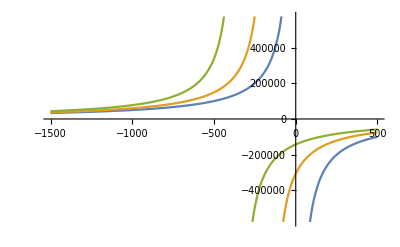

```mathematica
Plot[{α[2π(f88+f 10^6),2π f88,2π(7.5 10^3)]*norm,α[2π(f88+f 10^6),2π f86,2π(7.5 10^3)]*norm,α[2π(f88+f 10^6),2π f84,2π(7.5 10^3)]*norm},{f,-1500,500}]
```

```mathematica
α[(2π c)/(1064 10^-9),(2π c)/(461 10^-9)]*norm
```

230.849

```mathematica
I0=(5 10^3)/((10^-2)^2);
-1/(2ϵ0 c)Re[α[(2π c)/(1064 10^-9),(2π c)/(461 10^-9)]]I0 1/kB(20kHz)/10^-6
```

-0.0127693 kHz

```mathematica
α[(2π c)/(1064 10^-9),(2π c)/(461 10^-9)]*norm
```

230.849